```mathematica
raw="[ 1,  9,  9, 10, 10,  0, 11, 11, 12, 12,  2],
\t[13, 14, 14,  0, 15, 16, 17,  0, 18, 19, 20],
\t[13, 21, 21, 22, 23,  6, 24, 25, 18, 19, 20],
\t[26,  0, 27, 61, 62, 62, 63, 63, 28,  0, 29],
\t[26, 30, 31, 61, 64, 65, 66, 67, 32, 33, 29],
\t[ 0, 34,  5, 68, 69,  0, 70, 67,  7, 35,  0],
\t[36, 37, 38, 68, 71, 72, 73, 74, 39, 40, 41],
\t[36,  0, 42, 75, 75, 76, 76, 74, 43,  0, 41],
\t[44, 45, 46, 47, 48,  8, 49, 50, 51, 51, 52],
\t[44, 45, 46,  0, 53, 54, 55,  0, 56, 56, 52],
\t[ 4, 57, 57, 58, 58,  0, 59, 59, 60, 60,  3],";
```

```mathematica
field=Map[FromDigits,StringCases[StringSplit[raw,"\n"],DigitCharacter..],{2}]
```

{{1,9,9,10,10,0,11,11,12,12,2},{13,14,14,0,15,16,17,0,18,19,20},{13,21,21,22,23,6,24,25,18,19,20},{26,0,27,61,62,62,63,63,28,0,29},{26,30,31,61,64,65,66,67,32,33,29},{0,34,5,68,69,0,70,67,7,35,0},{36,37,38,68,71,72,73,74,39,40,41},{36,0,42,75,75,76,76,74,43,0,41},{44,45,46,47,48,8,49,50,51,51,52},{44,45,46,0,53,54,55,0,56,56,52},{4,57,57,58,58,0,59,59,60,60,3}}

```mathematica
field/.{x_Integer:>If[5≤x≤8,Style[x,Red],x]}//Grid
```

1 | 9 | 9 | 10 | 10 | 0 | 11 | 11 | 12 | 12 | 2
13 | 14 | 14 | 0 | 15 | 16 | 17 | 0 | 18 | 19 | 20
13 | 21 | 21 | 22 | 23 | 6 | 24 | 25 | 18 | 19 | 20
26 | 0 | 27 | 61 | 62 | 62 | 63 | 63 | 28 | 0 | 29
26 | 30 | 31 | 61 | 64 | 65 | 66 | 67 | 32 | 33 | 29
0 | 34 | 5 | 68 | 69 | 0 | 70 | 67 | 7 | 35 | 0
36 | 37 | 38 | 68 | 71 | 72 | 73 | 74 | 39 | 40 | 41
36 | 0 | 42 | 75 | 75 | 76 | 76 | 74 | 43 | 0 | 41
44 | 45 | 46 | 47 | 48 | 8 | 49 | 50 | 51 | 51 | 52
44 | 45 | 46 | 0 | 53 | 54 | 55 | 0 | 56 | 56 | 52
4 | 57 | 57 | 58 | 58 | 0 | 59 | 59 | 60 | 60 | 3

```mathematica
Image[Colorize[field],Magnification->32]
```

-Graphics-

```mathematica
(*
  3 4        ;
2 3 4   2 2 2;
2 1 1 4 4 2  ;
2 1 1 3 3 1  ;
1 2 2 2 1 1 1;
*)
```

```mathematica
corner=
{{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,2,0,0,0,0,0},
{0,3,4,0,1,3,0,0,0,0,0},
{2,3,4,0,2,2,2,0,0,0,0},
{2,1,1,4,4,2,0,0,0,0,0},
{2,1,1,3,3,1,0,0,0,0,0},
{1,2,2,2,1,1,1,0,0,0,0}}
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,2,0,0,0,0,0},{0,3,4,0,1,3,0,0,0,0,0},{2,3,4,0,2,2,2,0,0,0,0},{2,1,1,4,4,2,0,0,0,0,0},{2,1,1,3,3,1,0,0,0,0,0},{1,2,2,2,1,1,1,0,0,0,0}}

```mathematica
opposing=corner+Reverse[Reverse/@corner];
full=opposing+Transpose[Reverse/@opposing];
full//Grid
```

1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1
2 | 1 | 1 | 3 | 3 | 1 | 3 | 3 | 1 | 1 | 2
2 | 1 | 1 | 4 | 4 | 2 | 4 | 4 | 1 | 1 | 2
2 | 3 | 4 | 0 | 2 | 2 | 2 | 0 | 4 | 3 | 2
1 | 3 | 4 | 2 | 1 | 3 | 1 | 2 | 4 | 3 | 1
1 | 1 | 2 | 2 | 3 | 8 | 3 | 2 | 2 | 1 | 1
1 | 3 | 4 | 2 | 1 | 3 | 1 | 2 | 4 | 3 | 1
2 | 3 | 4 | 0 | 2 | 2 | 2 | 0 | 4 | 3 | 2
2 | 1 | 1 | 4 | 4 | 2 | 4 | 4 | 1 | 1 | 2
2 | 1 | 1 | 3 | 3 | 1 | 3 | 3 | 1 | 1 | 2
1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1

```mathematica
StringJoin[Riffle[StringJoin[ToString/@(Riffle[#,","]/.{0->" ",1->"t",2->"l",3->"d",4->"w",8->"S"})]&/@full,"\n"]]
```

t,l,l,l,t,t,t,l,l,l,t
l,t,t,d,d,t,d,d,t,t,l
l,t,t,w,w,l,w,w,t,t,l
l,d,w, ,l,l,l, ,w,d,l
t,d,w,l,t,d,t,l,w,d,t
t,t,l,l,d,S,d,l,l,t,t
t,d,w,l,t,d,t,l,w,d,t
l,d,w, ,l,l,l, ,w,d,l
l,t,t,w,w,l,w,w,t,t,l
l,t,t,d,d,t,d,d,t,t,l
t,l,l,l,t,t,t,l,l,l,t

```mathematica
Image[full/.(Rule@@@Transpose[{Range[4],List@@@(ColorData["HTML"]/@{"Tan","LightGray","DarkGray","White"})}]~Join~{0->{0,0,0},8->{1,0,0}}),Magnification->32]
```

-Graphics-

```mathematica
h=First[Dimensions[full]];
w=Last[Dimensions[full]];
map=ConstantArray[0,Dimensions[full]];
territories={};
adjacency={};
index=1;
floodFill[i_,j_,type_,idx_]:=
If[0<i≤h&&0<j≤w&&full[[i,j]]>0,
If[map[[i,j]]>0,
If[map[[i,j]]≠idx,
AppendTo[adjacency[[idx]],map[[i,j]]]
],
If[full[[i,j]]==type,
map[[i,j]]=idx;
AppendTo[territories[[idx]],{i,j}];
floodFill[i+1,j,type,idx];
floodFill[i-1,j,type,idx];
floodFill[i,j+1,type,idx];
floodFill[i,j-1,type,idx]]
]
]
Do[
If[full[[i,j]]<1,
map[[i,j]]=0,
If[map[[i,j]]==0,
AppendTo[territories,{}];
AppendTo[adjacency,{}];
floodFill[i,j,full[[i,j]],index++]
]],
{i,h},
{j,w}]
Do[AppendTo[adjacency[[j]],i],{i,index-1},{j,adjacency[[i]]}];
Do[adjacency[[i]]=Union[adjacency[[i]]],{i,index-1}]
```

```mathematica
(map-1)//Grid
territories//Grid
(adjacency-1)//Grid
```

0 | 1 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 4
5 | 6 | 6 | 7 | 7 | 2 | 8 | 8 | 9 | 9 | 10
5 | 6 | 6 | 11 | 11 | 12 | 13 | 13 | 9 | 9 | 10
5 | 14 | 15 | -1 | 12 | 12 | 12 | -1 | 16 | 17 | 10
18 | 14 | 15 | 19 | 20 | 21 | 22 | 23 | 16 | 17 | 24
18 | 18 | 19 | 19 | 25 | 26 | 27 | 23 | 23 | 24 | 24
18 | 28 | 29 | 19 | 30 | 31 | 32 | 23 | 33 | 34 | 24
35 | 28 | 29 | -1 | 36 | 36 | 36 | -1 | 33 | 34 | 37
35 | 38 | 38 | 39 | 39 | 36 | 40 | 40 | 41 | 41 | 37
35 | 38 | 38 | 42 | 42 | 43 | 44 | 44 | 41 | 41 | 37
45 | 46 | 46 | 46 | 43 | 43 | 43 | 47 | 47 | 47 | 48

{1,1} |  |  | 
{1,2} | {1,3} | {1,4} | 
{1,5} | {1,6} | {2,6} | {1,7}
{1,8} | {1,9} | {1,10} | 
{1,11} |  |  | 
{2,1} | {3,1} | {4,1} | 
{2,2} | {3,2} | {3,3} | {2,3}
{2,4} | {2,5} |  | 
{2,7} | {2,8} |  | 
{2,9} | {3,9} | {3,10} | {2,10}
{2,11} | {3,11} | {4,11} | 
{3,4} | {3,5} |  | 
{3,6} | {4,6} | {4,7} | {4,5}
{3,7} | {3,8} |  | 
{4,2} | {5,2} |  | 
{4,3} | {5,3} |  | 
{4,9} | {5,9} |  | 
{4,10} | {5,10} |  | 
{5,1} | {6,1} | {7,1} | {6,2}
{5,4} | {6,4} | {7,4} | {6,3}
{5,5} |  |  | 
{5,6} |  |  | 
{5,7} |  |  | 
{5,8} | {6,8} | {7,8} | {6,9}
{5,11} | {6,11} | {7,11} | {6,10}
{6,5} |  |  | 
{6,6} |  |  | 
{6,7} |  |  | 
{7,2} | {8,2} |  | 
{7,3} | {8,3} |  | 
{7,5} |  |  | 
{7,6} |  |  | 
{7,7} |  |  | 
{7,9} | {8,9} |  | 
{7,10} | {8,10} |  | 
{8,1} | {9,1} | {10,1} | 
{8,5} | {8,6} | {9,6} | {8,7}
{8,11} | {9,11} | {10,11} | 
{9,2} | {10,2} | {10,3} | {9,3}
{9,4} | {9,5} |  | 
{9,7} | {9,8} |  | 
{9,9} | {10,9} | {10,10} | {9,10}
{10,4} | {10,5} |  | 
{10,6} | {11,6} | {11,7} | {11,5}
{10,7} | {10,8} |  | 
{11,1} |  |  | 
{11,2} | {11,3} | {11,4} | 
{11,8} | {11,9} | {11,10} | 
{11,11} |  |  |

1 | 5 |  |  |  | 
0 | 2 | 6 | 7 |  | 
1 | 3 | 7 | 8 | 12 | 
2 | 4 | 8 | 9 |  | 
3 | 10 |  |  |  | 
0 | 6 | 14 | 18 |  | 
1 | 5 | 7 | 11 | 14 | 15
1 | 2 | 6 | 11 |  | 
2 | 3 | 9 | 13 |  | 
3 | 8 | 10 | 13 | 16 | 17
4 | 9 | 17 | 24 |  | 
6 | 7 | 12 |  |  | 
2 | 11 | 13 | 20 | 21 | 22
8 | 9 | 12 |  |  | 
5 | 6 | 15 | 18 |  | 
6 | 14 | 19 |  |  | 
9 | 17 | 23 |  |  | 
9 | 10 | 16 | 24 |  | 
5 | 14 | 19 | 28 | 35 | 
15 | 18 | 20 | 25 | 29 | 30
12 | 19 | 21 | 25 |  | 
12 | 20 | 22 | 26 |  | 
12 | 21 | 23 | 27 |  | 
16 | 22 | 24 | 27 | 32 | 33
10 | 17 | 23 | 34 | 37 | 
19 | 20 | 26 | 30 |  | 
21 | 25 | 27 | 31 |  | 
22 | 23 | 26 | 32 |  | 
18 | 29 | 35 | 38 |  | 
19 | 28 | 38 |  |  | 
19 | 25 | 31 | 36 |  | 
26 | 30 | 32 | 36 |  | 
23 | 27 | 31 | 36 |  | 
23 | 34 | 41 |  |  | 
24 | 33 | 37 | 41 |  | 
18 | 28 | 38 | 45 |  | 
30 | 31 | 32 | 39 | 40 | 43
24 | 34 | 41 | 48 |  | 
28 | 29 | 35 | 39 | 42 | 46
36 | 38 | 42 |  |  | 
36 | 41 | 44 |  |  | 
33 | 34 | 37 | 40 | 44 | 47
38 | 39 | 43 | 46 |  | 
36 | 42 | 44 | 46 | 47 | 
40 | 41 | 43 | 47 |  | 
35 | 46 |  |  |  | 
38 | 42 | 43 | 45 |  | 
41 | 43 | 44 | 48 |  | 
37 | 47 |  |  |  |

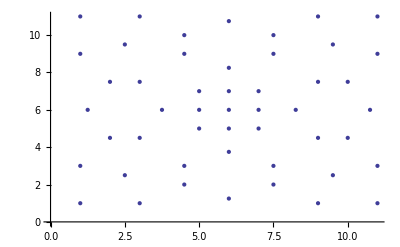

```mathematica
ListPlot[Mean/@territories]
```

```mathematica
Show[Colorize[map],Graph[Range[index-1],Flatten[Thread/@Thread[Range[index-1]->adjacency]],VertexCoordinates->(Mean/@territories-1/2)],ImageSize->(32 11)]
```

-Graphics-

```mathematica
Image[Colorize[map],Magnification->32]
```

-Graphics-